```mathematica
(* P3TMA Computer Project: From Fabry-Perot oscillations to Coulomb-blockade in a quantum wire *)
(* Author: Varvara Petrova *)
(* Code version : 1. Corresponds to the "NAIVE APPROACH" *)

(* ------------------ Paramètres ------------------ *)
Clear["Global`*"];
L=1000.;   (* distance entre les impuretés, L=x2-x1, en unités de a *)
ωmin=-0.010;   (* bords de l'intervalle de frequences, en unités de ωc *)
ωmax=0.010;
kF=0.;  (* vecteur(nombre) d'onde de Fermi, en unités de 1/a *)
Γ=0.1; (* Intensité du potentiel associé aux impurtetés, en unités aℏω_c. Hypothèse: ΓiF=ΓjB, pour tout i,j=1,2 *)
K=1.;(* Intensité d'interaction (coulombienne), K>0, sans dimension. En l'absence d'interaction, K=1.*)
γ=(K+1/K -2)/4.;
x1=-L/2; (* bords du domaine spatial, en unités de a *)
x2=L/2;
x12={x1, x2};
ε=1.*^-6; (* valeur de 0+ *)

(* ------------- Définition des fonctions ------------ *)
bar[i_]:=(If[i==1, Return[2]]; 1) ;

(* Eq.(8) de l'article (cf. reference [1] dans la bibliographie)
avec utilisation du résultat (B2) de l'appendice de la ref.54 pour le cas x=y *)
gR[r_, x_, y_, ω_]:=If[x≠y, 
-(Exp[I*r*kF*(x-y)]*(K^2)*(ω+I*ε)/(2.*Sqrt[Pi]*Gamma[1+γ]))*((2I*Abs[x-y]/(K*(ω+I*ε)) )^(0.5 - γ))*( BesselK[γ-0.5, -I*K*Abs[x-y]*(ω+I*ε)] - Sign[r*(x-y)]*BesselK[γ+0.5, -I*K*Abs[x-y]*(ω+I*ε)]),
-(Gamma[0.5-γ]*(K^2)*(ω+I*ε)/(4*Sqrt[Pi]*Gamma[1+γ]))*((-0.5*I*K*(ω+I*ε))^(2*γ-1))];

(* gR[-1, x2, x2, 0.005]*)

(* Eq.(12) de l'article: *)
bigD[r_,ω_]:=(1-Γ*gR[-r, x1, x1, ω])*(1-Γ*gR[-r, x2, x2, ω]) - Γ*gR[-r, x1, x2, ω]*Γ*gR[-r, x2, x1, ω];

(* bigD[1,0.005] *)

(* Eq.(13): *)
χ[r_,i_,j_,ω_]:=Γ*gR[r, x12[[i]],x12[[j]], ω] + 
(Γ*gR[r, x12[[i]],x12[[bar[j]]], ω]*Γ*gR[-r, x12[[bar[i]]],x12[[i]], ω]+
Γ*gR[r, x12[[i]],x12[[j]], ω]*Γ*gR[-r, x1,x2, ω]*Γ*gR[-r, x2,x1, ω]+
Γ*gR[r, x12[[i]],x12[[j]], ω]*Γ*gR[-r, x12[[i]],x12[[i]], ω]*(1-Γ*gR[-r, x12[[bar[j]]],x12[[bar[j]]], ω])
)/bigD[r,ω];

(*χ[-1,1, 2, 0.005]*)

(* Eq.(10): *)
GRrri[r_, i_, x_, ω_]:=(
(1-χ[r,bar[i],bar[i],ω])*gR[r, x12[[i]], x,ω]+χ[r,i,bar[i],ω]*gR[r, x12[[bar[i]]], x,ω]
)/(
(1-χ[r,1,1,ω])*(1-χ[r,2,2,ω])-χ[r,1,2,ω]*χ[r,2,1,ω]
);

(* GRrri[-1, 1, 250., 0.005] *)

(* Eq.(11): *)
GRmrri[r_, i_, x_, ω_]:=(
Sum[ gR[-r,x12[[i]], x12[[j]], ω]*Γ*GRrri[r,j, x, ω], {j,2}]+
Γ*Γ*(
gR[-r,x12[[i]], x12[[bar[i]]], ω]*gR[-r,x12[[bar[i]]], x12[[i]], ω]-
gR[-r,x12[[i]], x12[[i]], ω]*gR[-r,x12[[bar[i]]], x12[[bar[i]]], ω]
)*GRrri[r,i, x, ω]
)/bigD[r,ω];

(* GRmrri[-1, 1, x1, 0.005] *)

(* Eq.(7) *)
GRr1r2[r1_, r2_, x_, y_, ω_]:=If[r2==1, 
gR[r1, x, y, ω]*KroneckerDelta[r1,r2]+Γ*Sum[gR[r1, x, x12[[i]], ω]*(GRrri[1,i,y,ω]+GRmrri[1,i,y,ω]), {i,2}], 
gR[r1, x, y, ω]*KroneckerDelta[r1,r2]+Γ*Sum[gR[r1, x, x12[[i]], ω]*(GRrri[-1,i,y,ω]+GRmrri[-1,i,y,ω]), {i,2}]
]

(* GRr1r2[1,1,250, 300, 0.005] *)

(* Eq.(5) *)
ρ[x_,ω_]:=-Sum[
Im[GRr1r2[r1, r2, x,x, ω]],
{r1, {-1,1}}, {r2, {-1,1}}]/Pi

(* -------------- Plot -------------- *)
fig=DensityPlot[ρ[x,ω], {x, 2*x1,2*x2}, {ω, ωmin, ωmax}, PlotPoints->100, ColorFunction->ColorData["BlueGreenYellow"], PlotLegends->Automatic,FrameLabel->{Style["x/a", 18], Style["ω/ω_c", 18] }] 
(*Export["fig_K_1_gamma_1_esp_6.png",fig]*)
```

-Graphics-

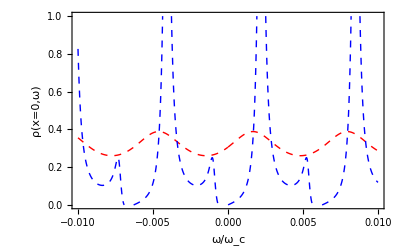

fig_K_1_gamma_0_1_1_esp_1_e6_x_0.png

```mathematica
ρx0[ω_]:=ρ[0,ω]
(* -------------- Plot Densité en fonction de l'énergie, position fixée------- *)
Γ=0.1;
p1=Plot[ρx0[ω],  {ω, ωmin, ωmax}, PlotStyle->{Red, Dashed, Thick}, Frame-> True, Axes-> True , FrameLabel->{Style["ω/ω_c", 18] , Style["ρ(x=0,ω)", 18]}, PlotRange-> {0,1}] ;
Γ=1.;
p2=Plot[ρx0[ω], {ω, ωmin, ωmax}, PlotStyle->{Blue, Dashed, Thick}, Frame-> True, Axes-> True , FrameLabel->{Style["ω/ω_c", 18] , Style["ρ(x=0,ω)", 18]}, PlotRange-> {0,1}] ;
(*Γ=10.;
p2=Plot[ρx0[ω], {ω, ωmin, ωmax}, PlotStyle->{Black}, Frame-> True, Axes-> True , FrameLabel->{Style["ω/ω_c", 18] , Style["ρ(x=0,ω)", 18]}, PlotRange-> {0,1}] ;*)
fig2=Show[p1, p2]
(*Export["fig_K_1_gamma_0_1_1_esp_1_e6_x_0.png",fig2]*)
```

```mathematica
(* Remarques et observations *)
(* χ peut être définie comme une matrice *)
(*χ=ConstantArray[0,{2,2}]; 
For[i=1,i≤2, i++,
For[j=1, j≤2, j++,
χ[[i,j]]=Γ*gR[r, x12[[i]],x12[[j]], ω] + 
(Γ*gR[r, x12[[i]],x12[[bar[j]]], ω]*Γ*gR[-r, x12[[bar[i]]],x12[[i]], ω]+
Γ*gR[r, x12[[i]],x12[[j]], ω]*Γ*gR[-r, x1,x2, ω]*Γ*gR[-r, x2,x1, ω]+
Γ*gR[r, x12[[i]],x12[[j]], ω]*Γ*gR[-r, x12[[i]],x12[[i]], ω]*(1-Γ*gR[-r, x12[[bar[j]]],x12[[bar[j]]], ω])
)/bigD[r,ω]
]
];*)
(* Cette définition de χ a posé des problèmes par la suite : évaluation des fonctions qui contiennent χ aboutit aux expressions semi-analytiques...à moins de pré-affecter les valeurs aux variables de ces fonctions et indiquer les mêmes valeurs dans les arguments, procédure impraticable si l'on veut faire des plots par la suite. *)
```